```mathematica
Needs["H3`","M3/src/H.m"];
Needs["H4`","M4/src/H.m"];
Needs["A4`","M4/src/A.m"];
```

```mathematica
genCircle[n_]:=(
	SeedRandom[0];
	{N[Table[{Cos[2π/n*i],Sin[2π/n*i]}*RandomReal[{0.7,1.3}],{i,n}]],Table[{i,Mod[i,n]+1},{i,n}]});
circle1=genCircle[100];
circlePT=preFair[P[circle1,2],Length[P[circle1,1]]];
```

```mathematica
Manipulate[Show[{showCurve[circle1],showCurve[fair[circle1,i,λ,κ,circlePT],RGBColor[1,0,0]]}],
	{{n,100,"Points"},Slider[Dynamic[n,(
		n=#;
		circle1=genCircle[#];
		circlePT=preFair[P[circle1,2],Length[P[circle1,1]]];)&],{10,100,1}]&},
	{{i,100,"iterations"},1,200,1},
	{{λ,.5},0,1},
	{{κ,.1},0,1}]
```

```mathematica
SBSMALL=Get["M4/dat/sphereBumpy_small.txt"];
SBBIG=Get["M4/dat/sphereBumpy_big.txt"];
```

```mathematica
Manipulate[Show[{showSurfaceEdgesOnly[SBSMALL,RGBColor[1,0,0]],showSurface[fair[SBSMALL,i,λ,κ],RGBColor[.5,.5,.5]]}],
	{{i,1,"iterations"},1,10,1},
	{{λ,.5},0,1},
	{{κ,.1},0,1}]
```

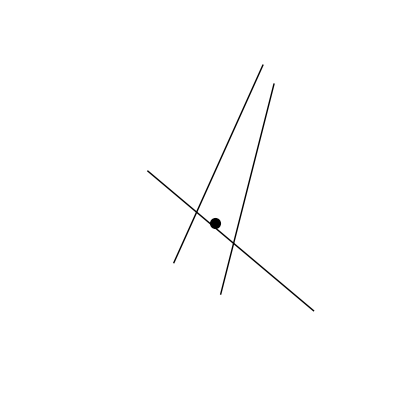

Minimizer location:{0.640767,0.292982}  QEM at minimizer: 0.0835043

```mathematica
(* line definition *)
SeedRandom[1];numLines=3;lines=Module[{α},Table[{{Random[],Random[]},α=RandomReal[{0,2π}];{Sin[α],Cos[α]}},{i,numLines}]];
(* call your code to compute QEM coefficients, its minimizer and QEM value *)
{p,e}=getMinimizerQEM[getCoefficients[lines]];
(* display the minimizer location and its QEM *)
perp[{x_,y_}]:={-y,x};Graphics[{Map[Line[{#⟦1⟧-perp[#⟦2⟧],#⟦1⟧+perp[#⟦2⟧]}]&,lines],PointSize[0.02],Point[p]},PlotRange->{{-1,2},{-1,2}}]
Print["Minimizer location:",p,"  QEM at minimizer: ",e];
```

```mathematica
(* Circle *)
numPoints=100;
circle={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]},{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

```mathematica
Manipulate[Show[showCurve[circle,RGBColor[1,0,0]],showCurveWithPoints[simplify2D[circle,n]]],{{n,20},3,100,1}]
```

```mathematica
(* Wavy circle *)
numPoints=100;
circleWave={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*(1+.2*Sin[10π/numPoints*i]),{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

```mathematica
Manipulate[Show[showCurve[circleWave,RGBColor[1,0,0]],showCurveWithPoints[simplify2D[circleWave,n]]],{{n,10},3,100,1}]
```

```mathematica
(* function to display a plane as a quad*)
normalize[v_]:=v/√(v.v);
gPlane[p_,norm_]:=Module[{upvec=normalize[Table[Random[],{3}]],xvec,yvec},
xvec=normalize[Cross[norm,upvec]];yvec=Cross[norm,xvec];
Polygon[Table[2*(Sin[α]xvec+Cos[α]yvec)+p,{α,0,2π,2π/4}]]];
```

```mathematica
(* plane definition *)
SeedRandom[0];numPlanes=5;
planes=Module[{α,β},Table[{{Random[],Random[],Random[]},
α=RandomReal[{0,2π}];β=RandomReal[{-π/2,π/2}];
{Sin[β]Sin[α],Sin[β]Cos[α],Cos[β]}},{i,numPlanes}]];
(* call your code to compute QEM coefficients, its minimizer and QEM value *)
{p,e}=getMinimizerQEM[getCoefficients[planes]];
(* display the minimizer location and its QEM *)
Graphics3D[{{Opacity[.5],Map[gPlane[#⟦1⟧,#⟦2⟧]&,planes]},PointSize[0.05],Point[p]},PlotRange->All,Boxed->False,RotationAction->Clip]
Print["Minimizer location:",p,"  QEM at minimizer: ",e];
```

-Graphics3D-

Minimizer location:{0.132088,-0.158482,0.509892}  QEM at minimizer: 0.210822

```mathematica
(* Bone2D *)
bone=Get["M4/dat/bone_2D.txt"];
```

824

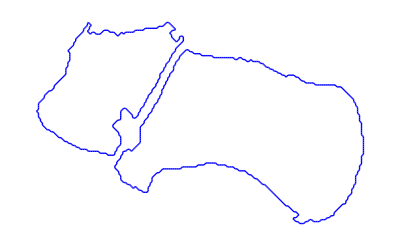

```mathematica
Length[P[bone,1]]
showCurve[bone]
```

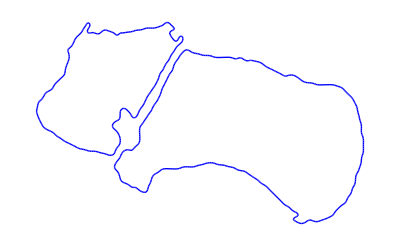

```mathematica
bonefair=fair[bone,20];
showCurve[bonefair]
```

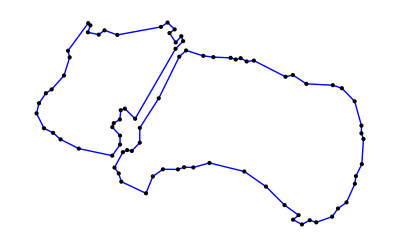

```mathematica
bonesim=simplify2D[bonefair,82];
showCurveWithPoints[bonesim,RGBColor[0,0,1]]
```

```mathematica
(* Bone3D *)
BONE=Get["M4/dat/bone_3D.txt"];
```

```mathematica
showSurface[BONE,RGBColor[.5,.5,.5]]
```

-Graphics3D-

```mathematica
BONEfair=fair[BONE,20]
showSurface[BONEfair,RGBColor[.5,.5,.5]]
```

-Graphics3D-